## Aula 2 - Treino

Métodos de valores numéricos para t entre (-1 a 3)

```mathematica
sol = NDSolve[{x'[t]==t* Exp[-x[t]], x[0]==1}, x[t], {t,-1,3}]
```

```mathematica
{{x[t]->InterpolatingFunction[{{-1., 3.}}, <>][t]}}
```

General::noinfo: Input expression InterpolatingFunction[{{-1., 3.}}, <>] contains insufficient information to interpret the result.

```mathematica
x[t]/.sol
```

{InterpolatingFunction[{{-1., 3.}}, <>][t]}

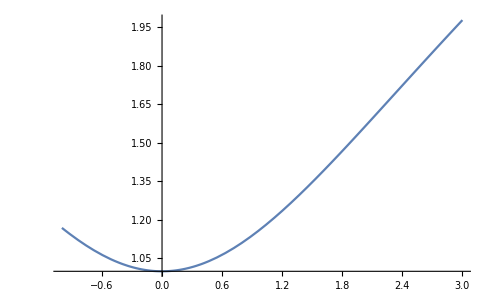

```mathematica
Plot [x[t]/.sol,{t,-1,3}]
```

```mathematica
solv = NDSolve[{x'[t]==t+ x[t]^2, x[0]==-1.3}, x[t], {t,-1,1}]
```

NDSolve::ndsz: At t == -0.801575, step size is effectively zero; singularity or stiff system suspected.

{{x[t]→InterpolatingFunction[{{-0.801575, 1.}}, <>][t]}}

InterpolatingFunction::dmval: Input value {-0.999959} lies outside the range of data in the interpolating function. Extrapolation will be used.

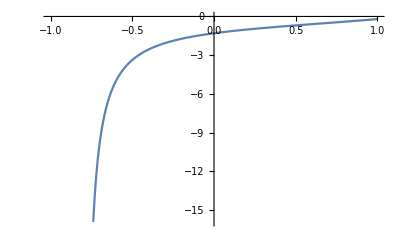

```mathematica
Plot [x[t]/.solv,{t,-1,1}]
```